# -Graphics-

# Writing a Wolfram Language Function

## Learning Objectives

### Motivation

Qualities of a “good” function

### The Basics

Standard function structure

Pure functions

### Arguments

Adding arguments

Restricting arguments

Adding optional arguments and defaults

### Options

Adding options to functions

Handling duplicated options

Filtering options

Restricting option names and values

### Extending Capability

Overload a function with multiple definitions

Make a function recursive or iterative

Use memoisation and caching for speed

Use upvalues to give a function different properties

Optional: operators and subvalues

### Error Handling

Exit a computation when there is a failure

Exit a computation manually

Error messages

Optional: Testing and debugging

### Useful Tips

Localise variables within a computation

Add syntax information to a function

Give a function special attributes

Speed and efficiency

Add a progress monitor to a computation

Extract information from a function

Common coding pitfalls

## Motivation

Wolfram Language has over 6,600 built-in functions:

```mathematica
Length[WolframLanguageData[]]
```

### Qualities of a Good Function

Generally speaking, a “good” function is one that:

is robust to all input (i.e. it is difficult to break)

gives a clear output (i.e. it does what you expect it to do)

is flexible (i.e. it has the potential to be applied in contexts beyond its original scope)

has clear documentation (i.e. it can be used and understood by others)

In other words, when presented with a well-designed function, you should be able to read and understand its documentation, apply it in a variety of contexts and receive the results you expect.

These are just guidelines, however; sometimes, for example, it is useful for a function to be deliberately inflexible, with few or no options. 
Functions of the form NameQ, for instance, often allow just one argument or no options:

```mathematica
TrueQ[E^(I π)==-1]
```

```mathematica
TrueQ[1==2]
```

```mathematica
IsomorphicGraphQ[-Graphics-,-Graphics-]
```

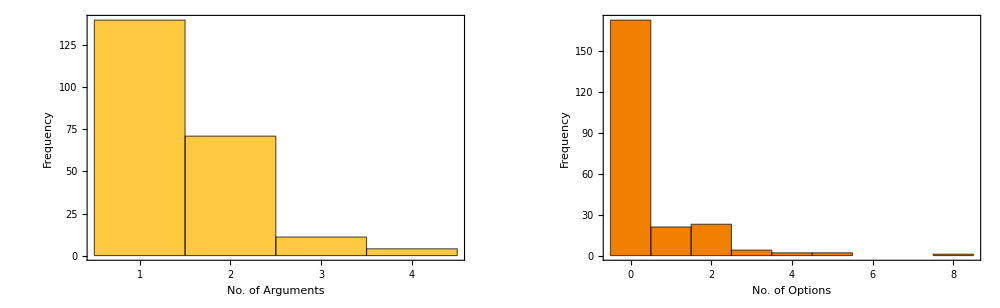
Wolfram Language Functions of the form 'NameQ'
-Graphics-

```mathematica
Column[
{
Style["Wolfram Language Functions of the form 'NameQ'", 15, Bold, GrayLevel[0.3]],
GraphicsRow[
{
Histogram[
Map[
Length[
DeleteCases[
Lookup[
SyntaxInformation[ToExpression[#]],
"ArgumentsPattern"
],
_OptionsPattern
]
]&,
Names["System`*Q"]
],
{1},
{Frame->True,FrameLabel->{{"Frequency",None},{"No. of Arguments",None}},FrameTicks->{{Automatic,None},{{0,1,2,3,4},None}},PlotRange->All}
],
Histogram[
Map[
Length[Options[ToExpression[#]]]&,
Names["System`*Q"]
],
{1},
{Frame->True,FrameLabel->{{"Frequency",None},{"No. of Options",None}},FrameTicks->{Automatic,None,{{0,1,2,3,4,5,6,7},None}},PlotRange->All,ChartStyle->RGBColor[0.95,0.5,0]}
]
},
ImageSize -> 1000
]
},
Alignment -> Center,
BaseStyle -> "Text"
]
```

## The Basics

### Function Structure

#### Standard Structure

The definition of a function typically takes the following form (mouse over the image for labels):

```mathematica
CellPrint[
ExpressionCell[
Mouseover[Framed[-Graphics-, RoundingRadius -> 5], Framed[-Graphics-, RoundingRadius -> 5]],
"Output",
GeneratedCell -> False,
CellMargins->{{Inherited, Inherited},{Inherited,Inherited}}
]
]
```

#### Common Practices

For readability, it is usually best to:

Use lowercaseCamelCase for the function name (and its arguments)

Use UppercaseCamelCase strings or symbols for any options

Other common conventions:

Use functionNameQ for functions that will always evaluate to True or False (e.g. EvenQ). (These functions are known as predicate functions.)

Use $name for global variables (e.g. $Version)

#### Quick Example

Here is an example of a function with one argument that multiplies the argument by three:

```mathematica
ClearAll[multiplyByThree];
multiplyByThree[num_] := num * 3;
```

These lines add the option to take the modulus of the result:

```mathematica
Options[multiplyByThree] = {"Modulus" -> 1};
multiplyByThree[num_, OptionsPattern[]]:=Mod[num * 3,OptionValue["Modulus"]];
```

Here is the function in action:

```mathematica
multiplyByThree[7]
multiplyByThree[7, "Modulus"->5]
```

## The Basics

### Pure Functions

The standard structure of a function definition requires you to give the function a name, which is not always desirable. The alternative—a pure function—has the benefit that it is defined in the same place it is used, meaning that someone reading your code will not have to go hunting for a definition.

#### Applications

You might want to use a pure function if your function is:

Simple

Only being used once

Forms part of a larger function

#### Forms

Pure functions come in a variety of forms, all of which use Function “under the hood”.

##### Function

Function is typically used in the form Function[parameters, body]:

```mathematica
Function[n, n^2][x]
```

```mathematica
Function[{p, q}, p + q][x, y]
```

The parameters can be dropped in favour of slots (#):

```mathematica
Function[#^2][x]
```

##### (body) &

A pure function can be shortened further by replacing Function[body] with (body)&:

```mathematica
(#^2)&[x]
```

Arguments can be referenced by their positions (# is equivalent to #1):

```mathematica
(#1^2)&[x]
```

```mathematica
(#2^2)&[x, y, z]
```

When applied to associations, slots can be referenced by labels:

```mathematica
(#b^2)&[<|"a" -> x,"b" -> y, "c" -> z|>]
```

##### f[slots] &

Pure functions can even be used as arguments for other functions:

```mathematica
f[#1, #2, #1*#2]&[x, y]
```

##### Optional: Additional Slot Notation

SlotSequence (##) refers to all of the arguments:

```mathematica
f[##]&[x, y, z]
```

##n refers to the n^th argument and all of the arguments after it:

```mathematica
f[##2]&[x, y, z]
```

While not common, a pure function can reference itself with #0:

```mathematica
f[#0]&[x]
```

#### Precedence

When code is evaluated, operators are applied sequentially according to their precedence. This can be thought of as an extension to mathematical precedence, where, for example, multiplication is applied before addition:

```mathematica
2 + 3 * 4
```

When using pure functions with an ampersand (&), it is usually best to include parentheses, both to make your intentions clear and to avoid errors.

Here, the pattern test (?) ‘binds more tightly’ than the function (&), so parentheses are required for the code to work properly:

```mathematica
Cases[{1,2,3,4,5},_?OddQ[#]&]
Cases[{1,2,3,4,5},_?(OddQ[#]&)]
```

In the first case, the kernel treats it like:

```mathematica
Cases[{1,2,3,4,5},(_ ? OddQ[#]) &]
```

This is testing for something nonsensical like “test whether the slot symbol itself is odd”.

This can be checked by looking at the full form:

```mathematica
FullForm[_?OddQ[#]&]
FullForm[_?(OddQ[#]&)]
```

## Arguments

### Implementing Arguments

Generally, arguments should be descriptive and lowerCamelCase. To add arguments to a function, put them (comma-separated) inside the square brackets:

```mathematica
ClearAll[takeLogarithm];
takeLogarithm[base_, value_]:=Log[base,value]
```

```mathematica
takeLogarithm[E,E^5]
```

```mathematica
takeLogarithm[10,1000]
```

Note that there are underscores after the arguments on the left-hand side, but not on the right.

A function can have no arguments at all. Even in this case, it is good practice to use square brackets to indicate that it is a function and not a variable.

```mathematica
ColorData[]
```

```mathematica
CurrentImage[]
```

## Arguments

### Restricting Arguments: Typical Approaches

Tech Note: Patterns and Transformation Rules

Restricting the arguments a function can take can make it more robust. It can also help someone to understand what the function is doing. Argument restriction is done with pattern matching, and there are a few common ways to do this.

#### Head

The simplest way to restrict an argument is to match a Head:

```mathematica
ClearAll[toUpperCase];
toUpperCase[string_String] := ToUpperCase[string];
toUpperCase["text"]
toUpperCase[notText]
```

#### Pattern Test

An alternative to matching a head is to use a PatternTest (?) with a predicate function:

```mathematica
ClearAll[redStyle];
redStyle[string_?StringQ] := Style[string, Red];
redStyle["text"]
redStyle[notText]
```

More complicated tests may require a pure function:

```mathematica
ClearAll[greenStyle];
greenStyle[string_?(StringQ[#]&&StringContainsQ[#, "go", IgnoreCase -> True]&)] := Style[string, Green];
greenStyle["text"]
greenStyle["textContainingGo"]
greenStyle[notText]
```

#### Pattern

A pattern can be assigned a label with Pattern (:):

```mathematica
ClearAll[blueStyle];
blueStyle[string:_String] := Style[string, Blue];
blueStyle["text"]
blueStyle[notText]
```

For simple patterns like this one, assigning a label is not really necessary. However, it can be very useful when patterns span multiple arguments (more on this later).

#### Condition

Another way to restrict an argument is to apply a Condition (/;) with a pattern test.

This can be done inside the square brackets:

```mathematica
ClearAll[fontStyle];
fontStyle[str_ /; StringQ[str]] := Style[str, FontFamily->"Algerian"];
fontStyle["text"]
fontStyle[notText]
```

…or outside the square brackets:

```mathematica
ClearAll[largeStyle];
largeStyle[str_] /; StringQ[str] := Style[str, 20];
largeStyle["text"]
largeStyle[notText]
```

For a condition with a complicated pattern test, applying it outside the square brackets usually makes the function easier to read. For a computationally expensive test, it may also make the function run slightly more quickly.

##### Optional: More Examples

A pattern or test can be as complex as you like.

Create a function that allows only a nested association with exactly n levels:

```mathematica
ClearAll[checkAssoc];
checkAssoc[assoc_Association, n_Integer] /;  SameQ[ArrayDepth[assoc, AllowedHeads -> Association], n] := assoc;
checkAssoc[<|a -> 1|>, 2]
checkAssoc[<|a -> <|b -> 1|>|>, 2]
checkAssoc[<|a -> <|b -> <|c -> 1|>|>|>, 2]
checkAssoc[{a -> {b -> 1}}, 2]
```

Create a function that only accepts a list containing a particular KeyValuePattern:

```mathematica
ClearAll[checkRule];
checkRule[rule:KeyValuePattern[_?(StringQ[#] && ! StringContainsQ[#, DigitCharacter]&) -> _Integer?(#>0&)]] := rule;
checkRule[{"a" -> 1}]
checkRule[{"123" -> 1}]
checkRule[{"a" -> -1}]
```

## Arguments

### Restricting Arguments: Multiple Arguments

Rather than restricting one argument at a time, you can apply a pattern to several arguments at once.

#### Pattern Sequences

Use BlankSequence (__) to match one or more expressions:

```mathematica
ClearAll[blendColors];
blendColors[colors__RGBColor] :=Blend[{colors},0.5] ;
blendColors[]
blendColors[RGBColor[1, 0, 0],RGBColor[0, 0, 1]]
```

Similarly, BlankNullSequence (___) will match zero or more expressions.

Use PatternSequence to match a particular sequence of arguments:

```mathematica
ClearAll[groupFirstTwoShapes];
groupFirstTwoShapes[firstTwo:PatternSequence[_,_],rest___] :=
TabView[
{
"First Two"->Graphics[{Hue[0.2],EdgeForm[Black],firstTwo}],
"Rest"->Graphics[{Hue[0.8],EdgeForm[Black],rest}]
}
];
groupFirstTwoShapes[RegularPolygon[10],RegularPolygon[3],RegularPolygon[5],RegularPolygon[6]]
```

Use OrderlessPatternSequence to allow a sequence of arguments to be given in any order:

```mathematica
ClearAll[power];
power[OrderlessPatternSequence[base_, index_Integer]] := base^index;
power[a, 2]
power[3, b]
```

#### Repeated Patterns

Use Repeated (..) to allow an argument to be repeated one or more times:

```mathematica
ClearAll[fluteSound];
fluteSound[expr:(_)..] := Sound[{"Flute",{expr}}];
fluteSound[]
fluteSound[SoundNote[0]]
fluteSound[SoundNote[0], SoundNote[0]]
```

Similarly, RepeatedNull (...) will allow zero or more arguments.

Note that a repeated Blank (_) does not mean that all of the arguments have to be the same:

```mathematica
fluteSound[SoundNote[0], SoundNote[1]]
```

To enforce this, you will need to name the expression being repeated:

```mathematica
ClearAll[fluteSound];
fluteSound[expr:(exprName_)..] := Sound[{"Flute",{expr}}];
fluteSound[SoundNote[0], SoundNote[0]]
fluteSound[SoundNote[0], SoundNote[1]]
```

fluteSound[SoundNote[0],SoundNote[1]]

##### Optional: More Examples

Allow just one or two arguments:

```mathematica
ClearAll[redStyle];
redStyle[item:Repeated[_, {1, 2}]] := Style[{item}, Red];
redStyle[]
redStyle[x]
redStyle[x, x]
redStyle[x, y]
redStyle[x, x, x]
```

redStyle[]

{x}

{x,x}

{x,y}

redStyle[x,x,x]

Allow lists of pairs:

```mathematica
ClearAll[redStyle];
redStyle[item:{_,_}..] := Style[{item}, Red];
redStyle[]
redStyle[{}]
redStyle[{a, b}]
redStyle[{a, b}, {c, d}]
redStyle[{a, b, c}, {d, e, f}]
```

redStyle[]

redStyle[{}]

{{a,b}}

{{a,b},{c,d}}

redStyle[{a,b,c},{d,e,f}]

## Arguments

### Optional Arguments and Default Values

Having to insert all the arguments of a function every time it is used can be inconvenient. One solution is to make the arguments optional, replacing them with default values when the arguments are omitted.

#### Optional

Use Optional (:) to make an argument optional and give it a default value:

```mathematica
ClearAll[borderingCountries]
borderingCountries[country_Entity,n_:2]:=
NestGraph[
#["BorderingCountries"] &,
country,
n,
VertexLabels -> Automatic
]
```

```mathematica
borderingCountries[Entity["Country","Switzerland"]]
```

```mathematica
borderingCountries[Entity["Country","Switzerland"],1]
```

As you may have noticed, the short form of Optional is the same as that for Pattern (a colon). However, it will usually be clear which is which from the context.

When using Pattern and Optional together, the pattern must go first:

```mathematica
ClearAll[borderingCountries]
borderingCountries[country_Entity,n:_Integer:2]:=
NestGraph[
#["BorderingCountries"] &,
country,
n,
VertexLabels -> Automatic
]
```

```mathematica
borderingCountries[Entity["Country","Switzerland"],1.3]
```

The syntax arg_?test:value is not permitted. If you want to apply a pattern test and have a default value, you must use Pattern:

```mathematica
ClearAll[badSyntax, goodSyntax];
badSyntax[arg_?IntegerQ : 1] := arg;
goodSyntax[arg:_?IntegerQ : 1] := arg;
badSyntax[3]
goodSyntax[3]
```

##### Optional: Default

One alternative to Optional is Default. While Optional indicates the optional property of an argument and its default value at the same time, Default separates these steps. Arguments that are optional are indicated inside the function with an underscore followed by a full stop (_.), and the corresponding default values are defined in a separate list.

Give the second argument of a function a default value:

```mathematica
ClearAll[anyStyle];
Default[anyStyle, 2] = Bold;
anyStyle[text_String, style_.] := Style[text, style];
anyStyle["Some text"]
anyStyle["Some text", Italic]
```

Some text

Some text

Give all arguments the same default value:

```mathematica
ClearAll[listZero];
Default[listZero] = 0;
listZero[x_., y_.] := {x, y};
listZero[]
listZero[a]
listZero[a, b]
```

{0,0}

{a,0}

{a,b}

Give the n^th argument a delayed default value based on its position:

```mathematica
ClearAll[listTwo];
Default[listTwo, n_] := 2*n;
listTwo[x_., y_., z_.] := {x, y, z};
listTwo[]
listTwo[a]
listTwo[a, b]
listTwo[a, b, c]
```

{2,4,6}

{a,4,6}

{a,b,6}

{a,b,c}

Use ClearAll to clear default values (Clear alone is not enough):

```mathematica
Clear[listZero, listTwo];
DefaultValues/@{listZero, listTwo}
```

{{HoldPattern[Default[listZero]]:>0},{HoldPattern[Default[listTwo,n_]]:>2 n}}

```mathematica
ClearAll[listZero, listTwo];
DefaultValues/@{listZero, listTwo}
```

{{},{}}

#### Overloading

Rather than specifying optional or default values, you can simply give a function multiple definitions. This is known as overloading (more on this later):

```mathematica
ClearAll[partyInvitation];
partyInvitation[]:="You're invited!"
partyInvitation[name_]:=name<>", you're invited!"
partyInvitation[name_,place_GeoPosition]:=name<>", you're invited to "<>ToString[place]<>"!"
partyInvitation[name_,place_GeoPosition,time_DateObject]:=name<>", you're invited to "<>ToString[place]<>" at "<>ToString[time]<>"!"
```

```mathematica
Column[
partyInvitation @@@ Rest[FoldList[Append,{},{"Wolfie",Here,Now}]]
]
```

## Options

### Adding Options

Adding options to a function provides a way to add extra functionality without cluttering the body of the function.

Generally, custom option names should be descriptive, UpperCamelCase strings. While functions like OptionValue often treat strings and symbols interchangeably, using strings avoids potential clashes with other symbols.

#### Managing Options

Guide: Options Management

Adding options to a function typically requires the use of three closely related functions: Options, OptionValue and OptionsPattern.

Options gives the list of default options assigned to a function:

```mathematica
Options[Plot]
```

OptionValue gives the value of a particular option:

```mathematica
OptionValue[Plot, AlignmentPoint]
```

OptionsPattern represents a collection of options given as a sequence or list of rules:

```mathematica
MatchQ[{"Option1"->optionValue1, "Option2" -> optionValue2}, OptionsPattern[]]
```

#### Standard Usage

Here is a typical setup using Options and OptionsPattern:

```mathematica
ClearAll[styleText];
Options[styleText] = {FontColor -> Red, FontWeight -> Bold};
styleText[text_, options:OptionsPattern[]]:=Style[text, options];
```

A named pattern (options) has been used on the left-hand side to enable the options to be inserted anywhere on the right-hand side.

When the function is evaluated, the default options are not used unless they are listed explicitly:

```mathematica
styleText["text"]
styleText["text", FontColor -> Red]
styleText["text", FontWeight -> Bold]
styleText["text", FontColor -> Red, FontWeight -> Bold]
```

You can, however, ensure that they are used by default:

```mathematica
ClearAll[styleText];
Options[styleText] = {FontColor -> Red, FontWeight -> Bold};
styleText[text_, options: OptionsPattern[]]:=Style[text, options, Sequence @@ Options[styleText]];
styleText["text"]
styleText["text", FontColor -> Blue, FontWeight -> Plain]
```

(Apply[Sequence, …] has been used here to replace the List head with Sequence.)

Rather than inserting all options in one place, you can pick and choose particular options to be used in different places. This is where OptionValue comes in:

```mathematica
ClearAll[styleText];
Options[styleText] = {FontColor -> Red, FontWeight -> Bold, "UpperCase" -> False};
styleText[string_, options : OptionsPattern[]] :=
Style[
If[
TrueQ[OptionValue["UpperCase"]],
ToUpperCase[string],
string
],
options,
FontColor -> OptionValue[FontColor]
];
styleText["text"]
styleText["text", FontColor -> Blue]
styleText["text", "UpperCase" -> True]
```

Option values can be delayed:

```mathematica
ClearAll[styleText];
Options[styleText] = {FontColor :> RandomColor[]};
styleText[text_, options:OptionsPattern[]]:=Style[text, options, FontColor -> OptionValue[FontColor]];
```

Test with multiple evaluations:

```mathematica
Do[
Echo[styleText["text"]],
5
]
```

#### Options vs Arguments

Without pattern restrictions, options may be misinterpreted as arguments.

Create a function that returns a styled word a number of times:

```mathematica
ClearAll[multiWord];
Options[multiWord]={"Colour" -> Red, "Weight" -> Plain};
multiWord[word_:"defaultWord",  repetitions_:1, OptionsPattern[]]:=
Style[
StringJoin[ConstantArray[word, repetitions]],
OptionValue["Colour"],
OptionValue["Weight"]
];
```

When only options are given, they are mistaken for arguments:

```mathematica
multiWord["Colour"->Blue,"Weight"->Bold]
```

StringJoin::string: String expected at position 1 in StringJoin[(Colour→color) Weight].

StringJoin[(Colour→RGBColor[0, 0, 1]) Weight→Bold]

Adding pattern restrictions to the arguments fixes this issue:

```mathematica
ClearAll[multiWord];
Options[multiWord]={"Colour" -> Red, "Weight" -> Plain};
multiWord[word_String:"defaultWord",  repetitions_Integer:1, OptionsPattern[]]:=Style[
StringJoin[ConstantArray[word, repetitions]],
OptionValue["Colour"],
OptionValue["Weight"]
];
multiWord["Colour" -> Blue, "Weight" ->Bold]
```

## Options

### Duplicated Options

In the case of duplicated options, only the first option value will be used.

Consider this definition of styleText from earlier, where the implicit options (options) are listed before the explicit options (Options[styleText]):

```mathematica
ClearAll[styleText];
Options[styleText] = {FontColor -> Red, FontWeight -> Bold};
styleText[text_, options: OptionsPattern[]]:=Style[text, options, Sequence@@Options[styleText]];
```

In this case, the function works as intended; adding new options changes the output:

```mathematica
styleText["text"]
styleText["text", FontColor -> Blue, FontWeight -> Plain]
```

text

text

However, if the order of the options is reversed, the explicit options take precedence instead:

```mathematica
ClearAll[styleText];
Options[styleText] = {FontColor -> Red, FontWeight -> Bold};
styleText[text_, options: OptionsPattern[]]:=Style[text, Sequence@@Options[styleText], options];
styleText["text"]
styleText["text", FontColor -> Blue, FontWeight -> Plain]
```

text

text

To be absolutely sure which option values are being used in a function, it is good practice to remove any duplicates:

```mathematica
ClearAll[styleText];
Options[styleText] = {FontColor -> Red, FontWeight -> Bold};
styleText[text_, options: OptionsPattern[]]:=
Style[
text, 
Sequence@@DeleteDuplicatesBy[Join[{options}, Options[styleText]], First]
];
```

```mathematica
styleText["text"]
styleText["text", FontColor -> Blue, FontWeight -> Plain]
```

text

text

## Options

### Filtering Options

Filtering options with FilterRules is a way to ensure that all the right options go to all the right parts of a function, making it more robust.

Create a function that takes a Graphics option as well as a custom title option:

```mathematica
ClearAll[titledGraphic];
Options[titledGraphic] = Join[Options[Graphics], {"Title" -> ""}];
titledGraphic[graphic_, options:OptionsPattern[]] := 
Column[
{
Text[OptionValue["Title"]],
Graphics[
graphic,
Sequence @@ FilterRules[{options}, Options[Graphics]]
]
},
Alignment -> Center
];
```

No matter the order in which they are used, options will be filtered to the relevant parts of the function:

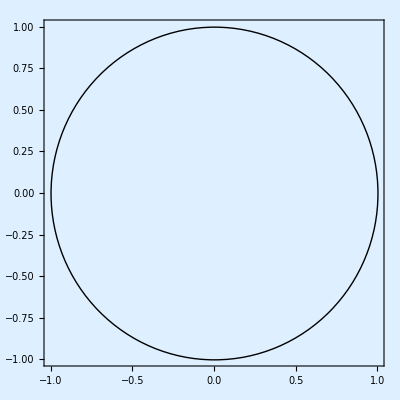
This is a circle
-Graphics-

```mathematica
titledGraphic[Circle[], Background -> LightBlue, "Title" -> "This is a circle", Frame -> True]
```

## Options

### Restricting Options

Another way to make a function more robust is to restrict the option names or values that can be used within it. This is typically done with Condition.

#### Option Names

Often, option names are required to be a members of a pre-defined list.

Require all option names of a function to be members of (the keys of) the default list of options:

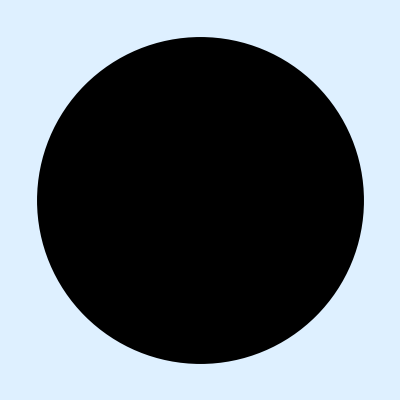

disk[{0,0},1,BadOption→value]

```mathematica
ClearAll[disk];
Options[disk] = Options[Graphics];
disk[centre_, radius_, options : OptionsPattern[]]/;ContainsAll[Keys[Options[disk]], Keys[{options}]]:=
Graphics[
{Disk[centre, radius]},
options
];
disk[{0, 0}, 1, Background -> LightBlue]
disk[{0, 0}, 1, "BadOption" -> value]
```

#### Option Values

Like arguments, option values are often required to be of a particular form (string, integer, etc.).

Require the value of a function’s “Colour” option to be a valid colour:

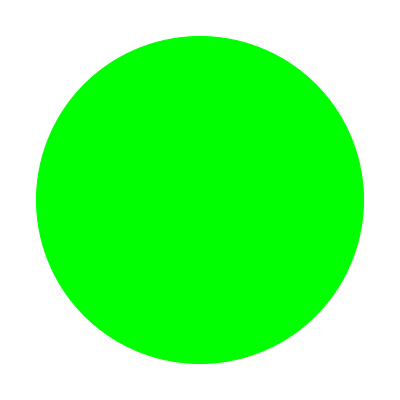

disk[{0,0},1,Colour→badColour]

```mathematica
ClearAll[disk];
Options[disk] = {"Colour" -> Red, "EdgeStyle" -> Thick};
disk[centre_, radius_, options : OptionsPattern[]]/;ColorQ[Lookup[{options}, "Colour", Black]]:=
Graphics[
{
EdgeForm[OptionValue["EdgeStyle"]],
OptionValue["Colour"],
Disk[centre, radius]
}
];
disk[{0, 0}, 1, "Colour" -> Green]
disk[{0, 0}, 1, "Colour" -> badColour]
```

Note that the default value for Lookup here (Black) won’t ever get called. It is used to ensure that ColorQ evaluates to True in the case of no options being provided.

We have not yet validated the “EdgeStyle” option value, hence:

```mathematica
disk[{0, 0}, 1, "EdgeStyle" -> badStyle]
```

## Extending Capability

### Overloading

Overloading a function simply means giving it multiple definitions for different types of input.

#### Standard Usage

Overloading is generally preferred over using a branching function like If, Which or Switch.

Round and square a number whether it is given as an integer, a fraction, a decimal or a string:

```mathematica
ClearAll[square];
square[integer_Integer] := integer^2;
square[fraction_Rational] := Round[Divide@@NumeratorDenominator[fraction]]^2;
square[decimal_Real] := Round[decimal]^2;
square[string_String] :=Round[Interpreter["SemanticNumber"][string]]^2;
```

```mathematica
square[23]
square[69/3]
square[23.4]
square["twenty three point four"]
```

Create a function to test the Collatz conjecture:

```mathematica
ClearAll[evenOddFun]
evenOddFun[number_?EvenQ]:=number/2;
evenOddFun[number_?OddQ]:=3*number+1;
evenOddFun[4]
evenOddFun[5]
```

#### Dependent Arguments

With the usual function syntax, the default value of one argument cannot be dependent on another argument:

```mathematica
ClearAll[f];
f[x_:1, y_ : x] := {x, y};
f[1]
```

However, this behaviour can be mimicked with overloading.

Create a function where the default value of the second argument equals the first argument:

```mathematica
ClearAll[f];
f[x_, y_ ] := {x, y};
f[x_:1] := {x, x};
f[]
f[a]
f[a, b]
```

##### Optional: Alternative Solutions

For this particular example, it would be clearer to do some recursion in the second definition, like so:

```mathematica
ClearAll[f];
f[x_, y_ ] := {x, y};
f[x_ : 1] := f[x, x];
```

Or you could localise the default value of the second argument:

```mathematica
ClearAll[f];
f[x_ : 1, y_ : dummy] := Block[{dummy = x}, {x, y}];
```

#### Dependent Option Values

The same principle can be applied to option values.

Create a function that puts a frame around a piece of text, where the rounding radius scales with the size of the frame margins:

```mathematica
ClearAll[frameText];
Options[frameText] =
DeleteDuplicatesBy[
Join[
{FrameMargins -> 10},
Options[Framed]
],
First
];
frameText[text_String, options:OptionsPattern[]]/;FreeQ[{options}, RoundingRadius] := 
Framed[
Text[text],
RoundingRadius -> OptionValue[FrameMargins]/2,
options
];
frameText[text_String, options:OptionsPattern[]] := Framed[Text[text], options];
frameText["text"]
frameText["text", FrameMargins -> 50]
frameText["text", RoundingRadius -> 10]
frameText["text", FrameMargins -> 50, RoundingRadius -> 10]
```

##### Optional: Alternative Solution

For this particular example, rather than overloading, it would be clearer to set the default value of RoundingRadius to a dummy value (e.g. Automatic), then make a replacement:

```mathematica
ClearAll[frameText];
Options[frameText] =
DeleteDuplicatesBy[
Join[
{FrameMargins -> 10, RoundingRadius -> Automatic},
Options[Framed]
],
First
];
frameText[text_String, options:OptionsPattern[]] := 
Framed[
Text[text],
RoundingRadius -> Replace[OptionValue[RoundingRadius], Automatic -> OptionValue[FrameMargins]/2],
Sequence @@ DeleteCases[{options}, RoundingRadius -> _]
];
```

#### Catch-Alls and Zero Arguments

Overloading is especially useful for creating a “catch-all”: a definition designed to handle any input types previously unaccounted for.

The square function defined earlier will not evaluate if the input is not an integer, fraction, decimal or string:

```mathematica
square[badInput]
```

Add a catch-all case:

```mathematica
square[___] := "Bad input – try again";
```

Additionally, rather than making every argument optional, overloading can be used to define a special zero-argument case:

```mathematica
square[] := "No arguments supplied";
```

The function will now handle all edge cases:

```mathematica
square[]
square[badInput]
```

## Extending Capability

### Recursion and Iteration

Recursive and iterative functions (often known as “self-referential” and “looping” functions, respectively) are useful for tasks that can be broken down into smaller subtasks. (Click here for an example of self-reference.)

#### Recursion

Recursive function definitions often use overloading. A classic example of recursion is computing the n^th Fibonacci number:

```mathematica
ClearAll[fibonacci];
fibonacci[1] := 1;
fibonacci[2] := 1;
fibonacci[n_Integer] := fibonacci[n-1]+fibonacci[n-2];
fibonacci[10]
```

Create a function to get the names and sizes of all files within a directory, regardless of its structure:

```mathematica
ClearAll[getFiles];
getFiles[filesOrDirectories_List] := Map[getFiles, filesOrDirectories];
getFiles[directory_?DirectoryQ] := getFiles[FileNames[All, directory]];
getFiles[file___] := FileNameTake[file] -> FileSize[file];
```

Apply the function to an example directory:

```mathematica
getFiles[ParentDirectory[NotebookDirectory[InputNotebook[]]]]
```

##### Optional: Alternative Solution

For this particular example, FileSystemMap does a similar job:

```mathematica
FileSystemMap[FileSize, exampleDirectory, Infinity]
```

#### Iteration: Looping Constructs

Guide: Looping Constructs

Looping constructs employ what might be called “standard” iteration. They are useful for carrying out tasks a predetermined number of times or until a test fails to give True. Often different looping constructs can be used to perform the same task.

While For is often the go-to function for creating loops in other languages, it is rarely used in the Wolfram Language; Do, Table and While are usually preferred.

Use Table to create a function that produces an m×nmatrix by iterating over m and n:

```mathematica
ClearAll[matrix];

matrix[m_, n_] :=Table[Subscript[a, i, j], {i, m}, {j, n}];

matrix[3, 4]
```

Create the same function with Do:

```mathematica
ClearAll[matrix];

matrix[m_, n_] :=Module[
{list = {}},
Do[AppendTo[list, Subscript[a, i, j]], {i, m}, {j, n}];
Partition[list, n]
];

matrix[3, 4]
```

Note that Do, unlike Table, does not return an output—hence the more verbose code in this case.

Use While to create a function that calculates the largest common factor of two numbers:

```mathematica
ClearAll[largestCommonFactor];

largestCommonFactor[num1_,num2_] := Module[
{a, b},
{a, b} = {num1, num2};
While[b≠0,{a, b} = {b, Mod[a, b]}];
a
];

largestCommonFactor[629, 1147]
```

Note that Do and Table localise their variables, but For and While do not (more on localisation later).

##### Optional: Alternative Solution

For this particular example, GCD does a better job:

```mathematica
GCD[629, 1147]
```

#### Iteration: Functional Iteration

Guide: Functional Iteration

Functional iteration is very similar to recursion and is carried out in much the same way: with overloading.

Create a function to find the remainder after dividing one number by another:

```mathematica
ClearAll[remainder];

remainder[number_, modulus_] /; Between[number, {0, modulus}] := number;
remainder[number_Integer?(#>0&), modulus_Integer?(#>0&)] :=remainder[number-modulus, modulus];

remainder[123456, 78]
```

##### Optional: Alternative Solution

For this particular example, it would be better to use Mod or QuotientRemainder:

```mathematica
Mod[123456, 78]
QuotientRemainder[123456, 78]
```

Functional iteration is easy to confuse with recursion. In functional iteration, the function being iterated must be the head of the expression on the right-hand side of the definition:

```mathematica
f["…"] := f[g["…"]]
```

In recursion, the function can appear anywhere on the right-hand side:

```mathematica
f["…"] := g[f["…"]]
```

For functional iteration (but not looping constructs), the number of levels of iteration is limited by the value of $IterationLimit:

```mathematica
ClearAll[f];

f[x_] := f[x+1];
f[1]
```

## Extending Capability

### Memoisation

Memoisation is a method of caching values to make iterative or recursive functions run more quickly.

Consider the recursive Fibonacci function created earlier:

```mathematica
ClearAll[fibonacci];

fibonacci[1] := 1;
fibonacci[2] := 1;
fibonacci[n_Integer] := fibonacci[n-1]+fibonacci[n-2];
```

In order to calculate the n^th Fibonacci number, it also has to calculate the result for n-1, n-2, …, 2, making it run more slowly the larger n gets:

```mathematica
RepeatedTiming[fibonacci[30];]
```

Incorporating memoisation makes the function much faster:

```mathematica
ClearAll[fibonacci];

fibonacci[1]:=1;
fibonacci[2]:=1
fibonacci[n_]:=fibonacci[n]=fibonacci[n-1]+fibonacci[n-2];

RepeatedTiming[fibonacci[30];]
```

The catch is that all these values have to be stored somewhere, so this solution would not be suitable for very large n:

```mathematica
DownValues[fibonacci]
```

##### Optional: Alternative Solution

A better solution here would be to use Fibonacci, which uses a formula rather than a recurrence relation:

```mathematica
Fibonacci[30]
```

## Extending Capability

### Caching

Once provides a way to cache expensive or time-consuming computations:

```mathematica
Once[Pause[3];RandomReal[]]
```

For further evaluations of the same expression, only the result from the first evaluation is given:

```mathematica
Once[Pause[3];RandomReal[]]
```

This can be utilised in a similar way to memoisation:

```mathematica
ClearAll[fibonacci];

fibonacci[1] := 1;
fibonacci[2] := 1;
fibonacci[n_Integer] := Once[fibonacci[n-1]+fibonacci[n-2]];

fibonacci[30]
```

However, once again, the values have to be stored somewhere:

```mathematica
PersistentObjects["Hashes/Once/*"]//Short
```

They can be deleted with DeleteObject:

```mathematica
DeleteObject[PersistentObjects["Hashes/Once/*"]]
```

##### Optional: Data Structure

If you wish to constrain the amount of stored values, you can use the data structure "LeastRecentlyUsedCache".

Create a Fibonacci function that caches just the last five values:

```mathematica
ClearAll[fibonacci, fibCache];

fibCache=CreateDataStructure["LeastRecentlyUsedCache",5];

fibonacci[1] := 1;
fibonacci[2] := 1;

fibonacci[x_]:=Block[
{compute,previous =fibCache["Lookup",x]},
If[
!MissingQ[previous],
previous,
(
compute = fibonacci[x-1]+fibonacci[x-2];
fibCache["Insert",x->compute];
compute
)
]
];
```

The function is very quick:

```mathematica
fibonacci[30]//RepeatedTiming
```

Check that only five values are being stored:

```mathematica
fibCache["Keys"]
```

## Extending Capability

### UpValues

Tutorial: Associating Definitions with Different Symbols

When a function is defined in the standard way, its definition is stored as a downvalue:

```mathematica
ClearAll[f];

f[x_] := x;

DownValues[f]
```

Sometimes it can be useful.08 for a function to behave differently when it is used in a particular context. TagSetDelayed (/:) can set up special definitions for a function when it is being used inside an expression. These definitions are then stored as upvalues:

```mathematica
ClearAll[f];

f/:expr[f[x_]] := x;

UpValues[f]
```

Note that f can only appear one level deep in the expression, or it will not be “found” by TagSetDelayed.

#### Standard Usage

##### Rule Systems

A good use of upvalues is for creating a “rule system” for a particular type of object.

Define your own version of logarithmic addition for positive numbers:

```mathematica
ClearAll[log];

log /: log[a_] + log[b_] := log[a*b];

log[3]+log[4]
```

Note that log[a*b] does not evaluate any further because log does not have any downvalues. If it did, they would disrupt the TagSetDelayed definition.

##### Databases

Another common use of upvalues is in setting up a “database” of properties for an object.

Many built-in objects work with Information, for example:

```mathematica
Information[InputNotebook[]]
```

(Information will be covered in more detail later.)

Create an arithmetic object from which various properties can be extracted:

```mathematica
ClearAll[arithmeticObject, summary, sum, product];

arithmeticObject /: summary[arithmeticObject[x_,y_]] := Dataset[<|"Var1" -> x, "Var2" -> y, "Sum" -> (x+y), "Product" -> (x * y)|>];
arithmeticObject /: sum[arithmeticObject[x_,y_]]:=x + y;
arithmeticObject /: product[arithmeticObject[x_,y_]]:=x * y;

summary[arithmeticObject[3,4]]
sum[arithmeticObject[3, 4]]
product[arithmeticObject[3, 4]]
```

##### Optional: A Box Trick

Like the log function before it, arithmeticObject cannot have any downvalues without disrupting the upvalues:

```mathematica
arithmeticObject//DownValues
arithmeticObject[3,4]
```

However, by using MakeBoxes and ToBoxes, you can get around this limitation.

Create a function that calculates some basic statistics from a list, using both upvalues and subvalues:

```mathematica
ClearAll[dataAnalyse];

dataAnalyse/:MakeBoxes[dataAnalyse[data_],form_]:=ToBoxes[Iconize[dataAnalyse[data], "Data"],form];

dataAnalyse/:Information[dataAnalyse[data : {_?NumericQ..}]]:=Dataset[
<|
"Mean" -> dataAnalyse[data]["Mean"],
"Length" -> dataAnalyse[data]["Length"],
"Properties" -> {"Properties", "Mean", "Length"}
|>
];

dataAnalyse[data : {_?NumericQ..}]["Mean"]:=Mean[data];
dataAnalyse[data_List]["Length"]:=Length[data];
dataAnalyse[data_]["Properties"]:={"Mean", "Length"};
```

The upvalues and subvalues perform as expected:

```mathematica
Information[dataAnalyse[{1,2,3}]]
```

```mathematica
dataAnalyse[{1, 2, 3}]["Mean"]
dataAnalyse[{1, 2, 3}]["Length"]
```

And the main definition works too:

```mathematica
dataAnalyse[{1, 2, 3}]
```

In fact, the iconised form is treated as if it were dataAnalyse itself:

```mathematica
["Mean"]
```

#### UpValues vs DownValues

Consider the following example, where an upvalue has been created for f:

```mathematica
ClearAll[f];

f/:Plus[f[a_], f[b_]] := f[a+b];
```

Rather than doing this, you could instead create a new downvalue for Plus*:

```mathematica
Plus[f[a_], f[b_]] := f[a+b]
```

However, since Plus is a built-in function—and fundamental to many other built-in functions!—changing its definition would be a very bad idea. As a general rule of thumb, it is better to create upvalues for less common functions than to create downvalues for more common ones.

*For this to work properly, you would need to apply Unprotect to Plus first.

## Extending Capability

### Optional: Operator Forms and Subvalues

Operator forms and (object) subvalues have similar syntax, but serve different purposes.

#### Operator Forms

Guide: Function Composition & Operator Forms

While functions are often applied to expressions by “wrapping around” them, an operator form of a function (if it exists) allows it to be applied as a Prefix. In this respect, an operator form acts a bit like a pure function.

Select, for example, has an operator form. 
Use Select on a list in the “regular” way:

```mathematica
Select[Range[10],EvenQ]
```

{2,4,6,8,10}

As an operator:

```mathematica
Select[EvenQ][Range[10]]
```

{2,4,6,8,10}

And as a pure function:

```mathematica
Select[#, EvenQ]& [Range[10]]
```

{2,4,6,8,10}

Defining an operator form of a function is very similar to defining a function in the usual way—there are just more square brackets involved:

```mathematica
ClearAll[listOperator];
listOperator[expr1_][expr2_] := List[expr1, expr2];
listOperator[x][y]
```

{x,y}

When a regular function is defined, the definition on the right-hand side of the SetDelayed symbol (:=) is stored as a DownValue for the function. When an operator form is defined, the definition is stored as a SubValue:

```mathematica
DownValues[listOperator]
SubValues[listOperator]
```

{}

{HoldPattern[listOperator[expr1_][expr2_]]:>{expr1,expr2}}

#### SubValues (of objects)

Sometimes, when the output of a function is large or cumbersome, it can be convenient to display it as an “object”:

```mathematica
SparseArray[{{1,1}->1,{2,2}->2,{3,3}->3}]
TimeSeries[{1, 2, 3}]
LinearModelFit[{{1, 2}, {3, 4}}, x, x]
Classify[{1 -> a, 2 -> b, 3 -> c}]
Iconize[{1, 2, 3}, "Data"]
```

SparseArray[…]

TimeSeries[…]

FittedModel[…]

ClassifierFunction[…]

This necessitates a mechanism to extract the object’s inner data. A typical function for doing this is Normal:

```mathematica
Normal[SparseArray[…]]
```

{{1,0,0},{0,2,0},{0,0,3}}

However, the problem with this is that it extracts all of the data at once—potentially thousands or millions of data points. Defining subvalues for an object provides a way around this, allowing small snippets of data to be extracted independently.

One place they are commonly used is in entities:

```mathematica
Entity["Planet","Jupiter"]["Satellites"]
```

Notice that the syntax for object subvalues is very similar to that of operator forms; the same can be said for how they are defined.

Create a function that produces an “arithmetic object”, then define subvalues for that object to extract its properties:

```mathematica
ClearAll[sumProd, arithmeticObject];
sumProd[x_, y_] := arithmeticObject[x, y];
arithmeticObject[x_,y_]["Properties"]:={"Properties", "Sum", "Product"};
arithmeticObject[x_,y_]["Sum"]:=x + y;
arithmeticObject[x_,y_]["Product"]:=x * y;
```

```mathematica
sumProd[3, 4]
```

```mathematica
arithmeticObject[3,4]["Sum"]
```

Note that arithmeticObject[x, y] on its own does not evaluate any further. This is because arithmeticObject does not have any downvalues. If it did, they would disrupt the subvalue definitions—but evaluation order is going beyond the scope of this course.

### Self-Reference

Click here for an example of self-reference.

## Error Handling

Errors are an inevitable part of programming. They are often unexpected, bewildering and can be tricky to track down.

### Flow Control: Exiting on Failures

Guide: Flow Control

An important part of error handling is catching errors before they can propagate to other parts of a program.

#### Confirm and Enclose

Confirm and Enclose can be used together to abort a computation if a “failure object” is received by Confirm. Recognised failure objects include Failure[…], Missing[…], $Failed, $Canceled and $Aborted.

Create a function that fails if a key is missing from an association:

```mathematica
ClearAll[lookup];
lookup[assoc_, key_] := Enclose[Confirm[Lookup[assoc, key]]];
lookup[<|1 -> a, 2 -> b, 3 -> c|>, 4]
```

Failure[…]

Create a function to calculate the square root of a number (using Newton's method) that fails if the calculation takes too long:

```mathematica
ClearAll[newtonSqrt];
newtonSqrt[num_, initialGuess_] :=
Enclose[
Confirm[
TimeConstrained[
FixedPoint[
(#+num/#)/2.&,
initialGuess
],
 1
]
]
];
newtonSqrt[15129, badGuess]
newtonSqrt[15129, 1.]
```

Failure[…]

123.

While Confirm is limited to a handful of failure types, there are several other Confirm-related functions with wider capabilities, all of which are supported by Enclose: Confirm, ConfirmBy, ConfirmMatch, ConfirmQuiet and ConfirmAssert.

Create a function that returns a number only if it is positive:

```mathematica
ClearAll[returnPositive];
returnPositive[number_] := Enclose[ConfirmBy[number, #>=0&]];
returnPositive[RandomInteger[{-10, 10}]]
```

Failure[…]

Returning a Failure object is not always desirable. The second argument of Enclose can be used to modify the output.

Create a custom version of StringTake that produces a failure message if the string has fewer characters than the number being taken:

```mathematica
StringTake["abc",4]
```

StringTake::take: Cannot take positions 1 through 4 in "abc".

StringTake[abc,4]

```mathematica
ClearAll[stringTake];
stringTake[string_,n_]:=
Enclose[
ConfirmQuiet[
StringTake[string,n]
],
ReleaseHold[#["HeldMessageCall"]]&
];
stringTake["Good string", 4]
stringTake["Short string", 100]
```

Good

StringTake::take: Cannot take positions 1 through 100 in "Short string".

##### Optional: Alternative Solution

In this particular case, a simpler approach would be to use UpTo:

```mathematica
StringTake["Short string", UpTo[100]]
```

##### Optional: Additional Properties

If there is no surrounding Enclose, ConfirmX functions will fail by default (and produce an error):

```mathematica
Confirm[anything]
```

Confirm::confirmnotag: Confirm has no tag or surrounding Enclose.

Failure[…]

If you want to use ConfirmX and Enclose “separately” (that is, where the confirmation is not directly surrounded by an Enclose), you will need to add (matching) tags:

```mathematica
ClearAll[confirmation];
confirmation := ConfirmBy[RandomInteger[{-10, 10}], #>=0&, Null, "tag"];
Enclose[confirmation, Identity, "tag"]
```

3

#### Check

Check can be used to return a different result if an error message is generated during a computation (a bit like an error-specific version of If):

```mathematica
Check[1/2; "NoError", "Error"]
Check[1/0; "NoError", "Error"]
```

NoError

Power::infy: Infinite expression 1/0 encountered.

Error

However, unlike Enclose/Confirm, it does not abort the computation:

```mathematica
Check[1/0; Print["PrintedError"], "Error"]
```

Power::infy: Infinite expression 1/0 encountered.

PrintedError

Error

Recreate the stringTake function, this time returning the original string if it is too short:

```mathematica
ClearAll[stringTake];
stringTake[string_, n_] := Check[StringTake[string,n],string];
stringTake["Good string", 4]
stringTake["Short string", 100]
```

Good

StringTake::take: Cannot take positions 1 through 100 in "Short string".

Short string

Check is often used in conjunction with Quiet to quieten all messages of a certain type.

Recreate the stringTake function, this time quietening any “take” error messages, but allowing other messages to print:

```mathematica
ClearAll[stringTake];
stringTake[string_, n_] := 
Quiet[
Check[StringTake[string,n],string, StringTake::take],
StringTake::take
];
stringTake["Good string", 4]
stringTake["Short string", 100]
stringTake[notAString, 1]
```

Good

Short string

StringTake::strse: A string or list of strings is expected at position 1 in StringTake[notAString,1].

StringTake[notAString,1]

## Error Handling

### Flow Control: More Exit Options

#### Throw and Catch

Throw and Catch work in a similar way to Confirm and Enclose, except the criteria for stopping a computation are more flexible. They are particularly useful for stopping loops early.

Create a function to find the next prime after a given number:

```mathematica
ClearAll[nextPrime];
nextPrime[startingPoint_, searchLength_] :=
Catch[
Do[
If[PrimeQ[i],Throw[i]],
{i,startingPoint, startingPoint + searchLength}
]
];
nextPrime[10^12, 50]
```

1000000000039

##### Optional: Mimicking Confirm/Enclose with Throw/Catch

Throw and Catch can be used to mimic the behaviour of Confirm and Enclose:

```mathematica
With[
{result=$Failed}, 
Catch[
If[FailureQ[result], 
Throw[error], 
result
]
]
]
```

error

However, the result in this case is not quite the same, since FailureQ does not catch all of the same failure objects as Confirm.

#### Break

Break will “exit” the nearest enclosing Do, For or While loop. Unlike Throw/Catch, this will not necessarily stop the computation (unless the loop is the outermost part of the program). Although less versatile than Throw/Catch, Break can also be used to stop a loop early.

Recreate the nextPrime function with Break and While:

```mathematica
ClearAll[nextPrime];
nextPrime[startingPoint_, searchLength_] := Module[
{i = startingPoint},
While[
i<startingPoint+searchLength,
(
If[PrimeQ[i],Break[]];
i++
)
];
i
]
nextPrime[10^12, 10]
```

1000000000010

(Note that this will print an incorrect result if no prime is found.)

##### Optional: Alternative Solution

A better solution than either of the nextPrime functions would be to use NextPrime:

```mathematica
NextPrime[10^12]
```

##### Optional: Additional Example

Create a custom version of PrimeQ that checks all of the factors less than the square root of a number:

```mathematica
ClearAll[primeQ];
primeQ[n_Integer?(#>3&)] :=
Module[
{tempDivisor = 2},
While[
tempDivisor <= Sqrt[n],
(
result = TrueQ[Divisible[n, tempDivisor]];
If[result, Break[], tempDivisor++]
)
];
Not[result]
];
primeQ[2354239]
```

True

#### Continue

Continue can be thought of as an opposite to Break. When a given criterion is met at a step inside a loop, instead of exiting the loop, Continue will “skip over” the current step and move onto the next one. Rather than a “single point” action (such as exiting a loop), Continue is better suited to performing an action several times.

Create a function that sums all of the (positive) odd integers less than or equal to a number:

```mathematica
ClearAll[oddTotal];
oddTotal[num_] :=
Module[
{sum=0},
Do[
(
If[EvenQ[i], Continue[]]; (* Skip every even integer *)
sum+=i
),
{i,num}
];
sum
];
oddTotal[1234 ]
```

380689

##### Optional: Mimicking Break with Continue

Although not recommended, Continue can be used (with While) to recreate the nextPrime function:

```mathematica
ClearAll[nextPrime];
nextPrime[startingPoint_, searchLength_] :=
Module[
{i = startingPoint, j=startingPoint+searchLength},
While[
i<j,
(
i++;
If[! PrimeQ[i],Continue[]]; (* Skip every composite number *)
j=i
)
];
j
]
nextPrime[10^12, 100]
```

1000000000039

Note that unlike the Throw and Break examples before it, this loop requires an extra parameter (j) to stop the loop.

## Error Handling

### Messages

Guide: Messages
Tech Note: Warnings and Messages

A very important part of error handling is explaining to the user what has gone wrong. This is usually done with error messages (along with good documentation).

#### Custom Messages

A custom message can be created using MessageName (::) and printed with Message. Information within a message can be curated with template values, where the syntax is similar to that used in StringForm:

```mathematica
function::messageTag = "This is an error message with two template values: `1` and `2`.";
Message[function::messageTag, "hello", "goodbye"]
```

Create a function that prints a message (unique to the input type) if the input is not a string:

```mathematica
ClearAll[stringToNum];

(* Messages: *)
stringToNum::num = "`1` is already a number.";
stringToNum::badArg = "`1` is a `2`. It should be a string.";

stringToNum[str_String] := Interpreter["SemanticNumber"][str];
stringToNum[num_?NumberQ] := (Message[stringToNum::num, num]; num);
stringToNum[sym_]/;(Message[stringToNum::badArg, sym, Head[sym]];False):="dummy";

stringToNum["twenty-two"]
stringToNum[22]
stringToNum[notAStringOrNumber]
```

Note the different return methods used for non-string inputs. When the input is a number, the number itself is returned* (along with a message). However, if the input is anything else, the function returns unevaluated. By using False in a Condition, the dummy output will never be returned.

*This is a fairly common approach, as is returning a failure object (such as $Failed) or nothing at all (Null).

#### Suppressing Messages

Quiet will suppress all messages during a calculation:

```mathematica
Quiet[stringToNum/@{123, x}]
```

However, a “suppress everything” approach is generally not a good idea. A better approach is to quiet only the messages you want to:

```mathematica
Quiet[stringToNum/@{123, x}, stringToNum::num]
```

The global behaviour of a message can be configured with On or Off (although these are mostly for debugging purposes):

```mathematica
Off[stringToNum::num];
stringToNum[5]
```

```mathematica
On[stringToNum::num];
stringToNum[5]
```

## Error Handling

### Optional: Testing and Debugging

#### Unit Testing

Workflow: Write Unit Tests
Tech Note: Using the Testing Framework

A typical way to check the behaviour of a function is simply to try many different types of input and see what happens:

```mathematica
ClearAll[fraction];
fraction[number_] := 1/number;
Column[Map[fraction, {-2, 0, 1/2, 2.0, "2", Infinity}]]
```

Power::infy: Infinite expression 1/0 encountered.

-1/2
ComplexInfinity
2
0.5
1/2
0

A more versatile approach is to use unit tests, which, among other things, allow you to specify the sorts of outputs you are expecting (including error messages):

```mathematica
tests = {
VerificationTest[fraction[-2], -1/2],
VerificationTest[fraction[0], ComplexInfinity, {Power::infy}],
VerificationTest[fraction[1/2], 2],
VerificationTest[fraction[2.0], 1/2],
VerificationTest[fraction["2"], fraction["2"]],
VerificationTest[fraction[Infinity], fraction[Infinity]]
}
```

{TestObject[…],TestObject[…],TestObject[…],TestObject[…],TestObject[…],TestObject[…]}

Carry out several tests at once with TestReport:

```mathematica
testReport = TestReport[tests]
```

TestReportObject[…]

Display the results of the report:

```mathematica
With[
{properties = First[testReport["TestResults"]]["Properties"]},
TabView[
Map[
#["Input"] -> Dataset[#[properties]] &,
Values[testReport["TestResults"]]
]
]
]
```

Rather than running these tests programmatically (as above), they can be run in a special test notebook (File ▶ New ▶ Programmatic Notebook ▶ Testing Notebook):

```mathematica
CellPrint[
ExpressionCell[
Button[
"Open new Testing Notebook",
CreateNotebook["Testing"],
BaseStyle -> "Text"
],
"Output",
GeneratedCell -> False
]
]
```

Open new Testing Notebook

While unit testing can seem a bit over the top for a single function, it can be very useful for testing several functions together (e.g. in a program or codebase).

#### Debugging

Guide: Tuning & Debugging

Tracking down an error can be a difficult and frustrating process. Two of the simplest and most common functions used in debugging are Echo and Trace. Mathematica also has built-in debugging tools (under Evaluation ▶ Debugger), but using them goes beyond the scope of this course.

##### Echo

With up to three arguments, Echo is like a super-charged version of Print.

Highlight values during a computation:

```mathematica
Total[
Table[
With[
{number=RandomReal[{-1, 1}]},
Echo[number, "Value:", If[number < 0, Style[#, Red], Style[#, Green]]&]
],
5
]
]
```

Value:  0.700875

Value:  0.34192

Value:  -0.602935

Value:  -0.489022

Value:  0.781822

0.73266

##### Optional: Alternative Solution

Rather than printing every value on a new line, Sow and Reap can be used to bundle them into a single list:

```mathematica
Reap[
Total[
Table[
With[
{number=RandomReal[{-1, 1}]},
If[number<0, Sow[number], number]
],
5
]
]
]
```

{-0.764461,{{-0.533368,-0.840614,-0.183909}}}

In a similar fashion, EchoTiming will print the duration of part of an evaluation.

Find the culprit in an unexpectedly long evaluation:

```mathematica
Table[EchoTiming[∫_0^∞ (∏_(k=0)^max Sin[x/(2 k+1)]/(x/(2 k+1)))ⅆx, "k = "<>ToString[max]],{max,6}]
```

"k = 1"  0.80366

"k = 2"  0.21152

"k = 3"  0.24222

"k = 4"  0.346657

"k = 5"  0.646928

"k = 6"  4.18379

{π/2,π/2,π/2,π/2,π/2,π/2}

Other EchoX functions include EchoEvaluation, EchoFunction and EchoLabel.

##### Trace

Trace will list every step in an evaluation in a list.

Track down the step at which a computation gives the wrong result due to a lack of precision:

```mathematica
Nest[11*#-2&, 0.2, 15] (* Result should be 0.2 *)
```

0.267457

```mathematica
Column[Trace[Nest[11*#-2&, 0.2, 15]]] (* List the evaluation steps *)
```

Nest[11 #1-2&,0.2,15]
{(11 #1-2&)[0.2],11 0.2-2,{11 0.2,2.2},2.2-2,0.2}
{(11 #1-2&)[0.2],11 0.2-2,{11 0.2,2.2},2.2-2,0.2}
{(11 #1-2&)[0.2],11 0.2-2,{11 0.2,2.2},2.2-2,0.2}
{(11 #1-2&)[0.2],11 0.2-2,{11 0.2,2.2},2.2-2,0.2}
{(11 #1-2&)[0.2],11 0.2-2,{11 0.2,2.2},2.2-2,0.2}
{(11 #1-2&)[0.2],11 0.2-2,{11 0.2,2.2},2.2-2,0.2}
{(11 #1-2&)[0.2],11 0.2-2,{11 0.2,2.2},2.2-2,0.2}
{(11 #1-2&)[0.2],11 0.2-2,{11 0.2,2.2},2.2-2,0.2}
{(11 #1-2&)[0.2],11 0.2-2,{11 0.2,2.2},2.2-2,0.2}
{(11 #1-2&)[0.2],11 0.2-2,{11 0.2,2.2},2.2-2,0.2}
{(11 #1-2&)[0.2],11 0.2-2,{11 0.2,2.2},2.2-2,0.200005}
{(11 #1-2&)[0.200005],11 0.200005-2,{11 0.200005,2.20005},2.20005-2,0.200051}
{(11 #1-2&)[0.200051],11 0.200051-2,{11 0.200051,2.20056},2.20056-2,0.200557}
{(11 #1-2&)[0.200557],11 0.200557-2,{11 0.200557,2.20613},2.20613-2,0.206132}
{(11 #1-2&)[0.206132],11 0.206132-2,{11 0.206132,2.26746},2.26746-2,0.267457}
0.267457

```mathematica
First[
With[ (* Find the first output with an error above some threshold: *)
{threshold = 10^-5},
Trace[Nest[11*#-2&, 0.2, 15], num_Real/;num-0.2>threshold, TraceDepth->3]
]
]
```

{0.200051}

##### Optional: Alternative Solution

In this particular example, NestList provides a more convenient way of getting all the outputs:

```mathematica
outputs = NestList[11*#-2&, 0.2, 15]
```

{0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.200005,0.200051,0.200557,0.206132,0.267457}

These can then be narrowed down with SelectFirst:

```mathematica
With[
{threshold = 10^-5},
SelectFirst[outputs, #-0.2>threshold&]
]
```

0.200051

## Useful Tips

### Localisation

Tech Note: Modularity and the Naming of Things
Guide: Scoping Constructs

A good practice for programming in general—not just for creating functions—is to localise variables wherever possible. There are three main functions for doing this: With, Module and Block. Each of these functions has a slightly different purpose, but for small tasks they are often interchangeable. Another function worth mentioning is DynamicModule, which is typically used for creating dynamic interfaces.

All of these functions share a common structure: a list of variables in the first argument and an expression (containing the variables) in the second argument.

#### With

Tech Note: Local Constants

With uses lexical scoping. It replaces its variables with their assigned values immediately, treating them like constants. Because of this, variables inside With cannot be reassigned:

```mathematica
With[{a = 1}, a = 2]
```

With is particularly useful for setting up initial data.

Create a function that plots some random temporal data (note the reuse of initialData several times throughout the function):

```mathematica
ClearAll[plotData];

plotData[noOfPoints_ : 100] := With[
{initialData = RandomFunction[ARProcess[{0.7},1],{1,noOfPoints}]},

ListPlot[
initialData,
PlotRange -> {{0, noOfPoints}, MinMax[initialData]+{-1,  1}},
PlotLegends -> Grid[
{
{"Mean", Mean[initialData]},
{"Range", First[Differences[MinMax[initialData]]]}
},

],

]
];

plotData[200]
```

#### Module

Tech Note: Modules and Local Variables
Tech Note: How Modules Work

Module uses lexical scoping. It is generally the go-to function for localising variables. To ensure there are no symbol conflicts, it creates new temporary symbols for each of its variables:

```mathematica
{Module[{a}, a], Module[{a}, a]}
```

Module can be used to localise small—so-called “helper”—functions, which can then be used inside larger functions.

Create a function that plots a distribution of Titanic passengers by age:

```mathematica
ClearAll[plotTitanicData];

plotTitanicData[{minAge_ : 20, maxAge_ : 30}] := With[
{data = Normal[ExampleData[{"Dataset","Titanic"}]]},
Module[
{deleteMissing, selectByAge},

(* Helper functions: *)
deleteMissing[data_] := Select[data, FreeQ[#, Missing[___]]&];
selectByAge[data_, interval_] := Select[data, Between[#["age"], interval] &];

(* Main function: *)
Histogram[
selectByAge[deleteMissing[data], {minAge, maxAge}][[All, "age"]],
{1},
PlotLabel -> StringForm["Distribution of passengers on the Titanic (aged `1` to `2`)", minAge, maxAge],
Frame -> True,
FrameLabel -> {"Age", "Frequency"},
ImageSize -> 500
]
]
];
```

```mathematica
plotTitanicData[{0, 20}]
```

```mathematica
Manipulate[
plotTitanicData[minMax],
{{minMax,100,"MinMax"},0,100,1},
ControlType->IntervalSlider
]
```

#### Block

Tech Note: Blocks and Local Variables
Tech Note: Blocks Compared with Modules

Block uses dynamic scoping. It sets up a miniature “global” environment in which the values of symbols can be temporarily reassigned. It is particularly useful for reassigning built-in constants.

Find the time in a different time zone:

```mathematica
Block[{$TimeZone = 7}, DateString[Now]]
```

Create a function that makes an engineering guesstimation for the volume of a planetary body by assuming that π = 3 and that the body is perfectly spherical:

```mathematica
ClearAll[planetaryVolume];

planetaryVolume[object_] := Block[{Pi = 3}, UnitConvert[Volume[Ball[{0, 0, 0}, object["Radius"]]], "Meters"^3]];
```

Estimate the volume of Jupiter and compare it to the true result:

```mathematica
planetaryVolume[Entity["Planet","Jupiter"]]
Entity["Planet","Jupiter"]["Volume"]
```

#### DynamicModule

Tech Note: Module versus DynamicModule
Tech Note: Introduction to Dynamic

DynamicModule uses lexical scoping. It is what Manipulate uses behind the scenes, and as such is very useful for creating custom dynamic interfaces (sliders, buttons, etc.). As the name suggests, it is like Module, but for dynamic variables. (However, there are subtle differences—see the first Tech Note above for more details.)

Create a labelled slider with some dynamic elements and insert it into a dynamic interface:

```mathematica
ClearAll[labelledSlider];

labelledSlider[Dynamic[x_], {min_ : 0, max_ : 1}, label_ : ""] := Row[
{
Pane[label, 150, Alignment -> Right],
Slider[Dynamic[x], {min, max}],
Dynamic[x]
},
Spacer[1],
BaseStyle -> "Text"
];

(* Interface: *)
DynamicModule[
{a =1, b = 1, c = 0, d = 0},
Column[{
Column[{
labelledSlider[Dynamic[a], {-5, 5}, "Vertical stretch:"],
labelledSlider[Dynamic[b], {-5, 5}, "Horizontal stretch:"],
labelledSlider[Dynamic[c], {-5, 5}, "Horizontal translation:"],
labelledSlider[Dynamic[d], {-5, 5}, "Vertical translation:"]
}],
Dynamic[Plot[a*Sin[b*x+c]+d, {x, -10, 10}, ]]
}]
]
```

Note the Dynamic wrapper in the first argument of labelledSlider. This serves two purposes: first, to enable the dynamic variable to be “scoped” by the DynamicModule; second, to make it clear to the user that the first argument is dynamic (there is no “DynamicQ” function in the Wolfram Language).

Here’s a version of the interface using Manipulate:

```mathematica
Manipulate[
Plot[
a*Sin[b*x+c]+d,
{x,-10,10},

],
{{a,1,"Vertical stretch"},-5,5},
{{b,1,"Horizontal stretch"},-5,5},
{{c,0,"Horizontal translation"},-5,5},
{{d,0,"Vertical translation"},-5,5}
]
```

#### Automatic Localisation

Many built-in functions localise their variables automatically (note the colouring of x):

```mathematica
Plot[x^2, {x, 0, 10}]
Table[x^2, {x, 1, 10}]
```

#### Other Localisation

Throw/Catch, Confirm/Enclose and Quiet/Check do some localisation behind the scenes to ensure a controlled transfer of information.

Several BeginX functions work with EndX functions to localise symbols. Compared to all of the other functions seen so far, these are somewhat unusual in that they do not use square brackets to enclose the things that are being localised.

Use Begin and End to create a function in the context MyContext`:

```mathematica
Remove[f];

Begin["MyContext`"];
f[x_] := x;
End[];
```

f does not have any information without the full context:

```mathematica
?f
?MyContext`f
```

Use BeginPackage and EndPackage to start and end a Wolfram Language package. These (together with Begin and End) are particularly useful for creating programs or codebases where symbol names are likely to conflict with those in the global context, or where definitions may need to be kept hidden from users. However, a full explanation goes beyond the scope of this course.

## Useful Tips

### Syntax Information

Function syntax refers to the allowed forms of a function—the patterns of arguments or options that are valid to use within it. If the allowed syntax has been defined for a function, invalid forms will be highlighted in red as the function is typed.

#### SyntaxInformation

A function’s syntax can be set with SyntaxInformation.

Specify that a function should take exactly one argument and zero options:

```mathematica
ClearAll[f];

SyntaxInformation[f]={"ArgumentsPattern"->{_}};
```

```mathematica
f[];
f[1,2];
```

Optional arguments can be set with the same notation seen in Default earlier: an underscore followed by a full stop (_.).

Specify that a function should have at least one argument, but not more than two:

```mathematica
SyntaxInformation[f]={"ArgumentsPattern"->{_, _.}};
```

```mathematica
f[1, 2, 3];
```

Specify that a function should take up to two arguments, plus some options:

```mathematica
Options[f] = {"a" -> 1, "b" -> 2};
SyntaxInformation[f]={"ArgumentsPattern"->{_, _., OptionsPattern[]}};
```

```mathematica
f[1, 2, "c" -> 3];
```

SyntaxInformation may not always be able to distinguish between arguments and options:

```mathematica
f[1, 2, 3, "a" -> 1];
f[1, 2, "123" -> 1];
```

Syntax information can be cleared with Unset (=.):

```mathematica
SyntaxInformation[f] =.;
```

#### CheckArguments

A function’s syntax can be checked (without evaluating it) with CheckArguments:

```mathematica
CheckArguments[f[1, 2, 3, "a" -> 1], {1, 2}]
CheckArguments[f[1, 2, "123" -> 1], {1, 2}]
```

CheckArguments allows arguments to be treated as options and vice versa:

```mathematica
CheckArguments[f[1, "c" -> 3], {1, 2}, <|"OptionsMode"->"Longest"|>] (* Treat "c" as an option *)
CheckArguments[f[1, "c" -> 3], {1, 2}, <|"OptionsMode"->"Shortest"|>] (* Treat "c" as an argument *)
```

## Useful Tips

### Attributes

Tutorial: Evaluation of Expressions

Rather than writing a general property into a function’s definition, some properties can be added as attributes:

```mathematica
Grid[
Thread[{
Map[
Button[
Mouseover[Style[#,"Hyperlink"],Style[#,"HyperlinkActive"]],NotebookLocate[{URL[StringJoin["https://reference.wolfram.com/language/ref/", #]],None}],
Appearance -> None
] &,
{
"Constant","Flat","HoldAll","HoldAllComplete","HoldFirst","HoldRest","Listable","Locked","NHoldAll","NHoldFirst","NHoldRest","NumericFunction","OneIdentity","Orderless","Protected","ReadProtected","SequenceHold","Stub","Temporary"
}
],
{
"all derivatives of f are zero",
"f is associative",
"all the arguments of f are not evaluated",
"the arguments of f are completely shielded from evaluation",
"the first argument of f is not evaluated",
"all but the first argument of f are not evaluated",
"f is automatically \"threaded\" over lists",
"attributes of f cannot be changed",
"the arguments of f are not affected by N",
"the first argument of f is not affected by N",
"all but the first argument of f are not affected by N",
"the value of f is assumed to be a number when its arguments are numbers",
"f[a], f[f[a]], etc. are equivalent to a in pattern matching",
"f is commutative",
"values of f cannot be changed",
"values of f cannot be read",
"Sequence objects in the arguments of f are not flattened out",
"Needs is automatically called if the symbol is ever input",
"f is a local variable, removed when no longer used"
}
}],
Sequence @@ 
]
```

| all derivatives of f are zero
 | f is associative
 | all the arguments of f are not evaluated
 | the arguments of f are completely shielded from evaluation
 | the first argument of f is not evaluated
 | all but the first argument of f are not evaluated
 | f is automatically "threaded" over lists
 | attributes of f cannot be changed
 | the arguments of f are not affected by N
 | the first argument of f is not affected by N
 | all but the first argument of f are not affected by N
 | the value of f is assumed to be a number when its arguments are numbers
 | f[a], f[f[a]], etc. are equivalent to a in pattern matching
 | f is commutative
 | values of f cannot be changed
 | values of f cannot be read
 | Sequence objects in the arguments of f are not flattened out
 | Needs is automatically called if the symbol is ever input
 | f is a local variable, removed when no longer used

(The full list can also be found here.)

Attributes gives the list of attributes associated with a function:

```mathematica
ClearAll[f];
Attributes[f]
```

This list can be overwritten:

```mathematica
Attributes[f]={Listable};
Attributes[f]
```

With the Listable attribute, a function will “thread over” a list argument automatically:

```mathematica
f[{a, b, c}]
Log[{a, b, c}]
```

Use SetAttributes to add to the list of existing attributes without overwriting it:

```mathematica
SetAttributes[f,Orderless];
Attributes[f]
```

With the Orderless attribute, a function will sort its arguments (this is similar to OrderlessPatternSequence seen earlier):

```mathematica
{f[a, b], f[b, a]}
{Plus[a, b], Plus[b, a]}
```

Clear one or more attributes of a function with ClearAttributes:

```mathematica
ClearAttributes[f, {Listable}];
Attributes[f]
```

Note that attributes generally apply to all arguments of a function (with some exceptions, like HoldFirst), so they should be considered carefully.

Consider the following function, which multiplies a vector by a scale factor. If the second argument is a list (of scale factors), it maps over it:

```mathematica
ClearAll[scaleVector];

scaleVector[vector_, scaleFactor_?NumberQ] := scaleFactor*vector;
scaleVector[vector_, scaleFactors_List] := Map[scaleVector[vector, #] &, scaleFactors];

scaleVector[{1, 2}, 2]
scaleVector[{1, 2}, {3, 4}]
```

Attempting to recreate the function using the Listable attribute makes for shorter code:

```mathematica
ClearAll[scaleVector];

Attributes[scaleVector] = {Listable};
scaleVector[vector_, scaleFactor_] := scaleFactor*vector;

scaleVector[{1, 2}, 2]
scaleVector[{1, 2}, {3, 4}]
```

However, the result is incorrect because the function now threads over both its arguments.

## Useful Tips

### Optional: Speed and Efficiency

While a full lesson in how to write faster code goes beyond the scope of this course, here are some general tips taken from this Wolfram Blog post (some of which you have seen already).

#### 1. Use Decimals

Use reals instead of integers to give faster (but potentially less accurate) results.

Calculate the determinant of a 100×100 matrix:

```mathematica
N[Det[Table[1/(1+Abs[i-j]), {i, 1, 100}, {j, 1, 100}]]];//RepeatedTiming
```

```mathematica
N[Det[Table[1./(1+Abs[i-j]), {i, 1, 100}, {j, 1, 100}]]];//RepeatedTiming
```

Depending on the type of input, some functions may use entirely different methods to arrive at the same result.

With real input, Solve will use numerical methods:

```mathematica
Solve[a*x^4+b*x^3+c*x+d == 0, x] /. {a -> 2., b -> 4., c -> 7., d -> 11.};//RepeatedTiming
```

```mathematica
Solve[a*x^4+b*x^3+c*x+d == 0 /. {a -> 2., b -> 4., c -> 7., d -> 11.}, x];//RepeatedTiming
```

#### 2. Compile

Use Compile to convert Wolfram Language code into faster machine code.

Do a simple calculation 10 000 times:

```mathematica
ClearAll[funct, compiledFunct];

funct = Function[
{x},
Block[
{sum = 1., inc = 1.}, 
Do[
(
inc = inc*x/i;
sum = sum + inc
),
{i, 10^4}
]
]
];

compiledFunct = Compile[
{x},
Block[
{sum = 1., inc = 1.}, 
Do[
(
inc = inc*x/i;
sum = sum + inc
),
{i, 10^4}
]
]
];
```

```mathematica
data = Range[-10, 10, 0.25];

Map[funct, data];//Quiet//RepeatedTiming
```

```mathematica
Map[compiledFunct, data];//RepeatedTiming
```

#### 3. Use Built-in Functions

Use built-in functions/algorithms where possible—they are almost always faster.

Flatten 10 million 2×2 lists into 1×4 lists:

```mathematica
data = RandomReal[1, {10^7, 2, 2}];

Map[Flatten, data];//RepeatedTiming
```

```mathematica
Flatten[data, {{1}, {2, 3}}];//RepeatedTiming
```

#### 4. Use an IDE / Debugging Tools

For large projects, use an Integrated Development Environment (IDE) for easier code management. For precise navigation through buggy code, use Mathematica’s debugging tool (under Evaluation ▶ Debugger):

```mathematica
Grid[{
Map[
Image[#, ImageSize -> {Automatic, 500}]&,
{-Graphics-, -Graphics-}
]
}]
```

-Graphics- | -Graphics-

(This particular IDE shown above is IntelliJ IDEA, for which there is a Wolfram Language plugin available. Debugging was covered earlier.)

The following IDEs are supported:

```mathematica
Grid[
{
MapThread[
Hyperlink[
Column[
{#1, #2},
Alignment -> Center,
Spacings -> 1
],
#3
]&,
{
{-Graphics-, -Graphics-, -Graphics-},
{"VSCode", "IntelliJ", "Eclipse"},
{"https://code.visualstudio.com/", "https://www.jetbrains.com/idea/", "https://eclipseide.org/release/"}
}
]
},
Alignment -> Bottom,
BaseStyle -> "Text",
Spacings -> {3, Automatic}
]
```

[-Graphics-
VSCode](https://code.visualstudio.com/) | [-Graphics-
IntelliJ](https://www.jetbrains.com/idea/) | [-Graphics-
Eclipse](https://eclipseide.org/release/)

#### 5. Memoise

Memoise functions to cache previous outputs.

Map all of the coordinates in an n×n grid:

```mathematica
ClearAll[gridPoints, gridPointsMemoised];

gridPoints[{m_, n_}] /; m<=0||n<=0 := {0, 0};
gridPoints[{m_, n_}] := gridPoints[{m-1, n}] + gridPoints[{m, n-1}];

gridPointsMemoised[{m_, n_}] /; m<=0||n<=0 := {0, 0};
gridPointsMemoised[{m_, n_}] := gridPointsMemoised[{m, n}] = gridPointsMemoised[{m-1, n}] + gridPointsMemoised[{m, n-1}];
```

```mathematica
gridPoints[{10, 10}];//RepeatedTiming
```

```mathematica
gridPointsMemoised[{10, 10}];//RepeatedTiming
```

##### Optional: Plotting grid points

Recreate the functions, this time sowing the grid points and plotting them:

```mathematica
ClearAll[gridPoints, gridPointsMemoised];

gridPoints[{m_, n_}] /; m<=0||n<=0 := {0, 0};
gridPoints[{m_, n_}] := Module[{a,b}, {a, b} = {m, n}; Sow[{a, b}]; gridPoints[{m-1, n}] + gridPoints[{m, n-1}]];

gridPointsMemoised[{m_, n_}] /; m<=0||n<=0 := {0, 0};
gridPointsMemoised[{m_, n_}] := gridPointsMemoised[{m, n}] = Module[{a,b}, {a, b} = {m, n}; Sow[{a, b}]; gridPointsMemoised[{m-1, n}] + gridPointsMemoised[{m, n-1}]];

With[
{n = 7},
Map[
ListLinePlot[
Reap[#[{n, n}]][[2, 1]],
PlotRange -> {{0, n + 1}, {0, n + 1}},
GridLines -> {Range[n], Range[n]},
Epilog -> {PointSize[0.02], Point[Tuples[Range[n], 2]]},

] &,
{gridPoints, gridPointsMemoised}
]
]
```

(Memoisation was covered earlier.)

#### 6. Parallelise

Run calculations in parallel with ParallelX functions:

```mathematica
LaunchKernels[]
```

```mathematica
Table[PrimeQ[x], {x, 10^1000, 10^1000+1000}];//RepeatedTiming
```

```mathematica
ParallelTable[PrimeQ[x], {x, 10^1000, 10^1000+1000}];//RepeatedTiming
```

```mathematica
CloseKernels[]
```

#### 7. Use Sow and Reap

When working with lists, use Sow and Reap instead of Append/AppendTo or Prepend/PrependTo:

```mathematica
(
data = {};
Do[
AppendTo[data, RandomReal[x]],
{x, 0, 10^3}
];
data
);//RepeatedTiming
```

```mathematica
(
data = Reap[
Do[
Sow[RandomReal[x]],
{x, 0, 10^4}
]
][[2, 1]]
);//RepeatedTiming
```

(Sow and Reap work in a similar way to Throw and Catch.)

If you prefer the style of AppendTo, use associations instead of lists. This is not as fast as Sow and Reap, but appends in constant time, rather than time proportional to the length of the data:

```mathematica
(
dataAssoc=<||>;
key=0;
Do[
AppendTo[dataAssoc,key++->RandomReal[x]],
{x,0,10^4}
];
data = Values[dataAssoc]
);//RepeatedTiming
```

#### 8. Use Block or With

Use Block or With instead of Module:

```mathematica
Do[Module[{x = 2.}, 1/x], {10^6}];//RepeatedTiming
Do[Block[{x = 2.}, 1/x], {10^6}];//RepeatedTiming
Do[With[{x = 2.}, 1/x], {10^6}];//RepeatedTiming
```

#### 9. Use Stricter Pattern Matching

Use tighter patterns for faster searches—or avoid them altogether:

```mathematica
data = RandomReal[1, 300];

(* Loose patterns: *)
ReplaceRepeated[data, {a___, b_, c_, d___}/;b>c :> {a, c, b, d}];//RepeatedTiming
```

```mathematica
(* No patterns at all: *)
(
flag = True;
While[
TrueQ[flag],
(
flag = False;
Do[
If[
data[[i]] > data[[i+1]],
(
temp = data[[i]];
data[[i]] = data[[i + 1]];
data[[i + 1]] = temp;
flag = True
)
],
{i, 1, Length[data] - 1}
]
)
];
data
);//RepeatedTiming
```

#### 10. Try Alternative Methods

If one method is not getting fast enough results, try a different one:

```mathematica
(
temp = 1;
Do[
temp = temp*i,
{i, 2^16}
];
temp
);//RepeatedTiming
```

```mathematica
Apply[
Times,
Range[2^16]
];//RepeatedTiming
```

## Useful Tips

### Progress Monitoring

Even with optimal code, a function may take some time to evaluate. During such an evaluation, it can be reassuring to see that something is happening—or better yet, to know how long it will take to finish.

#### Monitoring

Monitor allows you to temporarily display a dynamic object during an evaluation. A typical object to display is a ProgressIndicator, the duration of which can be known (“determinate”) or unknown (“indeterminate”).

Create a function that returns all of the prime numbers within a range, displaying a (determinate) dynamic progress bar while it is running:

```mathematica
ClearAll[primesBetween];

primesBetween[{min_, max_}] := Module[
{i = min},
Reap[
Monitor[
While[
Between[i, {min, max}],
If[PrimeQ[i], Sow[i]];
i++
],
ProgressIndicator[i, {min, max}]
]
][[2, 1]]
];
```

```mathematica
primesBetween[{0, 10^6}]
```

Create a function that returns the birthday of a famous figure, displaying an indeterminate “loading necklace” while it is running:

```mathematica
ClearAll[birthday];

birthday[person_String] :=Monitor[
Enclose[
With[
{personEntity = Interpreter["Person"][person]},
StringJoin[
Confirm[personEntity["Name"]],
" (",
StringDelete[ToString[Confirm[personEntity["Occupation"]]], {"{", "}"}],
") was born on ",
DateString[Confirm[personEntity["BirthDate"]]],
"."
]
],
#["Expression"]&
],
ProgressIndicator[Appearance -> "Necklace"]
];
```

```mathematica
birthday["nicola tesla"]
```

#### Temporary Printing

PrintTemporary is essentially a more basic version of Monitor.

Create a function that temporarily prints the steps of an application’s build process (where, in this case, steps are mimicked with Pause):

```mathematica
ClearAll[buildApplication];

buildApplication[] := (
PrintTemporary["Searching for updates…"];
Pause[1];
PrintTemporary["Downloading updates…"];
Pause[1];
PrintTemporary["Rendering interface…"];
Pause[1];
"Done!"
);
```

```mathematica
buildApplication[]
```

#### Other Monitoring Options

Some functions like StepMonitor and EvaluationMonitor have monitoring built in.

Print the steps of FindRoot as it searches for a solution:

```mathematica
Clear[x]; FindRoot[x^2-2,{x,1},EvaluationMonitor:>Print[x]]
```

Sow and reap the steps in order to plot them:

```mathematica
With[
{data = Reap[FindRoot[x^2-2,{x,1},StepMonitor:>Sow[x-Sqrt[2]]]][[2, 1]]},
ListLogPlot[data, Joined -> True]
]
```

##### Optional: StepMonitor vs EvaluationMonitor

To quote the documentation, StepMonitor is

"…an option for iterative numerical computation functions that gives an expression to evaluate whenever a step is taken by the numerical method used."

while EvaluationMonitor is

“…an option for various numerical computation and plotting functions that gives an expression to evaluate whenever functions derived from the input are evaluated numerically."

Generally, the expression given to EvaluationMonitor is evaluated more frequently than that of StepMonitor. This is easiest to show by example.

Consider the following expression:

```mathematica
(x-1)^2+100*(y-x^2)^2
```

Suppose you want to minimise it for real values of x and y. Since the expression is of the form a^2+100 b^2, and anything squared is always positive, the smallest value it can be is 0. Using Solve verifies that there is a solution in this case:

```mathematica
Solve[(x-1)^2+100*(y-x^2)^2==0, {x, y}, Reals]
```

However, suppose you did not know the minimum value you were aiming for. In that case, you could use FindMinimum to both find the minimum value and solve for x and y. Moreover, you could use StepMonitor and EvaluationMonitor to track how it arrived at its solution:

```mathematica
Clear[x, y];
{solution, monitorData} = Reap[
FindMinimum[
(x-1)^2+100*(y-x^2)^2,
{{x,-1},{y,0}}, (* Initial guesses for x and y *)
StepMonitor:> Sow[{x,y},"Steps"],
EvaluationMonitor:>Sow[{x,y},"Evaluations"]
],
_,
Rule
]
```

The monitored steps are a subset of the monitored evaluations:

```mathematica
Map[
ContourPlot[
(x-1)^2+100*(y-x^2)^2,
{x,-2,2},
{y,-5,2},
PlotLabel -> #,
Epilog->{
{Green, PointSize[0.05], Point[{x,y} /. solution[[2]]]},
{Yellow, PointSize[0.02], Point[#/.monitorData]}
},
ImageSize -> 400,
PlotRange -> All
] &,
{"Steps", "Evaluations"}
]
```

## Useful Tips

### Extracting Information

Tech Note: Getting Information about Wolfram Language Objects

While full details about how a function works should be written up in documentation, key properties (definitions, options, etc.) can be extracted programmatically.

#### Function Information

The quickest way to get information about a function is to use Information. For symbols, it has a convenient short form (??).

Get information about Dataset:

```mathematica
Information[Dataset]
??Dataset
```

Under the hood, an Information object is an association with keys that can be extracted:

```mathematica
Information[Dataset]//Keys
```

Extract the options of Dataset:

```mathematica
Options[Dataset]
Information[Dataset, "Options"]
```

Information has another short form (?) for extracting usage messages.

Create a usage message for scaleVector (using the MessageName notation seen earlier) and extract it:

```mathematica
scaleVector::usage = "scaleVector[v, c] scales a vector v by a factor of c.";

Information[scaleVector, "Usage"]
?scaleVector
```

Definition will print a function’s attributes, default values, options and (unless the function is read-protected) definitions:

```mathematica
Definition[Dataset]
```

(FullDefinition will also give any dependent definitions, if they exist.)

##### Optional: Styling Usage Messages

Messages are usually plain strings, but they can be styled:

```mathematica
scaleVector::usage = ToString[
StringForm[
"`1``2`, `3``4` scales a vector `2` by a scale factor of `3`.",
Style["scaleVector[", "Input"],
Style["v", Italic],
Style["c", Italic],
Style["]", "Input"]
],
StandardForm
]
```

#### Object Data

Information (in its long form) will also extract data from most objects:

```mathematica
Information[Databin["1qGFQ8v"]]
Information[Entity["City",{"London","GreaterLondon","UnitedKingdom"}]]
```

As seen earlier, Normal can often be used to get data out of an object. Another trick is to replace the head of the object using Apply and List:

```mathematica
object = TimeSeries[{1,2,3}, {{4,5,6}}]
```

```mathematica
Normal[object]
List@@object
```

#### Function Names

Information can be used with asterisks (*) to find all the function names that match a particular form (where an asterisk represents zero or more characters).

Find all of the functions that contain the word “List” (case-sensitive):

```mathematica
?*List*
```

Use Names to get a similar result:

```mathematica
Names["*List*"]
```

Although Names does not format the result as nicely, it is more flexible because it allows string patterns.

Get only functions that contain “List” followed by an uppercase character (thus avoiding words like “Listen”):

```mathematica
Names[(___~~"List")|(___~~"List"~~_?UpperCaseQ~~___)]
```

#### Output Forms

Tech Note: Forms of Input and Output

By default, expressions are output in StandardForm, but there are many other forms too:

```mathematica
?System`*Form
```

To get the underlying expression, you can use InputForm (or, for an even “deeper” look, FullForm):

```mathematica
({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}})//InputForm
```

```mathematica
-Graphics-//InputForm
```

## Useful Tips

### Common Pitfalls

In no particular order, here are some final tips and things to be aware of when writing a function.

#### Overloading

Use overloading rather than a branching function (If, Which, Switch, …).

When overloading, be careful about the ordering of function definitions. For custom functions with multiple definitions, the Wolfram Language will check for the more specific definitions before going to the generic definition. When the generality of definitions is not determined, the Wolfram Language will store and try definitions in the order that the definitions were created.

Include a catch-all definition.

#### Error Catching

Catch errors as early as possible.

If using branching functions, supply default values and ensure that all tests give Boolean results (True or False):

```mathematica
Clear[x];

If[TrueQ[x>0], 1, 2]
```

```mathematica
If[x>0, 1, 2, defaultValue]
```

```mathematica
Which[TrueQ[x>0], a, TrueQ[x<0], b, True, defaultValue]
```

```mathematica
Switch[x, _?(TrueQ[#>0]&), a, _?(TrueQ[#<0]&), b, _, defaultValue]
```

Use default argument/option values to ensure that a function always evaluates.

#### Function Choice

Use Do, Table, etc. instead of For.

When modifying lists, use Sow and Reap instead of Append, AppendTo, etc.

Use Replace with a level specification instead of ReplaceAll:

```mathematica
ReplaceAll[{{{a, a}}, {{a}}, {{a, a, a}}}, {a -> b}]
```

```mathematica
Replace[{{{a, a}}, {{a}}, {{a, a, a}}}, {a -> b}, {3}]
```

Do not use Return.

Use Cases and Select properly:

If your test is a function, you should use Select.

If your test is a pattern, you should use Cases.

If you need to change/transform the elements while extracting them, you should use Cases.

If it can be a mix of a pattern and a test function, Cases is better.

#### Code Writing

If working on a large project, use an IDE to manage your code.

Generally, readable code is preferred over slightly faster/more compact code.

Format your code: use white space; use new lines; choose a spacing convention (tabs or spaces) and stick with it.

Comment your code!

Give your functions usage and error messages (and, if relevant, documentation).

Localise variables.

Use full symbol names instead of shorthand (e.g. Map instead of /@).

Use parentheses for clarity (especially when pattern matching or writing a CompoundExpression).

## Course Summary

Creating a basic function is easy; creating a function that is flexible, robust, intuitive and powerful is not. In this course, you have learned about:

Function structure: qualities of a good function, common practices, pure functions

Argument structure: implementation, restriction (pattern matching), optional arguments, default values, operator forms, subvalues

Option structure: implementation, restriction, duplication, filtering

Coding methods: overloading, recursion and iteration, memoisation, caching, upvalues

Error handling: flow control, messages, testing, debugging

Localisation, syntax information, attributes, progress monitoring, information extraction, speed and efficiency